# Fourier

```mathematica
makeFourierGraph[freqs_,sinCoeffsInit_,cosCoeffsInit_,offsetFixed_]:=Module[
{nFourier,layerDefns,layerConn,graph}
,
nFourier=Length[freqs];

If[nFourier≠0
,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],

(* Freqs, coeffs *)
"cosCoeff"->NetArrayLayer["Output"->nFourier,"Array"->cosCoeffsInit],
"sinCoeff"->NetArrayLayer["Output"->nFourier,"Array"->sinCoeffsInit],
"freqs"->NetArrayLayer["Output"->nFourier,LearningRateMultipliers->None,"Array"->freqs],

(* Norm *)
"range"->FunctionLayer[Max[1,Total[Abs[#sinCoeff]]+Total[Abs[#cosCoeff]]+10^-8]&],

(* FT *)
"ft"->FunctionLayer[#offset+(Total[#sinCoeff*Sin[(#tpt-1)*#freqs]]+Total[#cosCoeff*Cos[(#tpt-1)*#freqs]])/#range&,"tpt"->1,"freqs"->nFourier,"sinCoeff"->nFourier,"cosCoeff"->nFourier,"offset"->1],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->NetPort["ft","offset"],

(* Norm *)
"sinCoeff"->NetPort["range","sinCoeff"],
"cosCoeff"->NetPort["range","cosCoeff"],

(* Remaining FT *)
"freqs"->NetPort["ft","freqs"],
"sinCoeff"->NetPort["ft","sinCoeff"],
"cosCoeff"->NetPort["ft","cosCoeff"],
"range"->NetPort["ft","range"],
"ft"->"ftFlatten"
};

,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->"ftFlatten"
};

];

graph=NetGraph[layerDefns,layerConn];
Return[graph]
]
```

```mathematica
minMax[x_,nFourier_]:=Map[Max[-1.0/nFourier,Min[1.0/nFourier,#]]&,x];
```

## Test

```mathematica
freqsTest={1,2,3,3};
sinCoeffsInit={-0.008,0.03,0.02,0.01};
cosCoeffsInit={0.001,0.05,0.001,0.005};
offsetFixed={1.0};

graph=makeFourierGraph[freqsTest,sinCoeffsInit,cosCoeffsInit,offsetFixed];
```

0.125

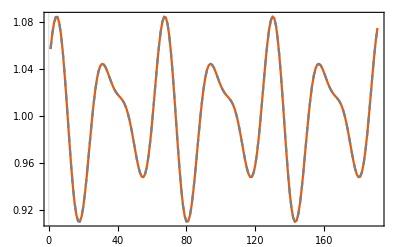

```mathematica
tptsPlt=Table[tpt,{tpt,1,20,0.1}];

range=Total[Abs[sinCoeffsInit]+Abs[cosCoeffsInit]]+10^-8
Show[
ListLinePlot[Table[graph[<|"tpt"->{tpt}|>],{tpt,tptsPlt}]],
ListLinePlot[Table[offsetFixed[[1]]+(Sum[sinCoeffsInit[[i]]*Sin[freqsTest[[i]]*(tpt-1)]+cosCoeffsInit[[i]]*Cos[freqsTest[[i]]*(tpt-1)],{i,Length[freqsTest]}])/Max[range,1],{tpt,tptsPlt}],PlotStyle->{Gray,Dashed}],
PlotRange->All
]
```

# Inverse

```mathematica
inverse1Layer[]:=FunctionLayer[#^-1&,"Input"->{1,1}];
```

```mathematica
inverse2Layer[]:=Module[
{layerConn,layerDefns}
,
layerDefns=<|
"denom"->FunctionLayer[-#mat[[1,2]]*#mat[[2,1]]+#mat[[1,1]]*#mat[[2,2]]&,"mat"->{2,2}],
"inverse"->FunctionLayer[{
{#mat[[2,2]]/#denom,-#mat[[1,2]]/#denom},
{-#mat[[2,1]]/#denom,#mat[[1,1]]/#denom}
}&,"mat"->{2,2}]
|>;
layerConn={
"denom"->NetPort["inverse","denom"]
};
Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
testMat={{1,3},{4,5}}//N;
inverse2Layer[][testMat]
Inverse[testMat]
```

{{-0.714286,0.428571},{0.571429,-0.142857}}

{{-0.714286,0.428571},{0.571429,-0.142857}}

# Convert params layer

```mathematica
convertbLayer[]:=FunctionLayer[#b1+Flatten[Transpose[#wt1].#muh1]-Transpose[#wt1].Sqrt[#varh1].(Sqrt[#varh2]^-1).#muh2&,"b1"->2,"wt1"->{1,2},"muh1"->{1,1},"varh1"->{1,1},"varh2"->{1,1},"muh2"->1]
```

```mathematica
convertwtLayer[]:=FunctionLayer[(Sqrt[#varh2]^-1).Sqrt[#varh1].#wt1&,"wt1"->{1,2},"varh1"->{1,1},"varh2"->{1,1}]
```

## Test

```mathematica
b1Test={1,2};
wt1Test={{3,4}};
muh1Test={3};
varh1Test={{3}};
varh2Test={{5}};
muh2Test={2};
b2True=b1Test+Transpose[wt1Test].muh1Test-Transpose[wt1Test].Sqrt[varh1Test].Inverse[Sqrt[varh2Test]].muh2Test//N
b2Actual=convertbLayer[][<|
"b1"->b1Test,
"wt1"->wt1Test,
"muh1"->muh1Test,
"varh1"->varh1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{5.35242,7.80323}

{5.35242,7.80323}

```mathematica
wt1Test={{3,4}};
varh1Test={{3}};
varh2Test={{5}};
wt2True=Inverse[Sqrt[varh2Test]].Sqrt[varh1Test].wt1Test//N
wt2Actual=convertwtLayer[][<|
"wt1"->wt1Test,
"varh1"->varh1Test,
"varh2"->varh2Test
|>]
```

{{2.32379,3.09839}}

{{2.32379,3.09839}}

## Convert params layer from 0

```mathematica
convertbLayerFrom0[]:=FunctionLayer[#b1-Transpose[#wt1].(Sqrt[#varh2]^-1).#muh2&,"b1"->2,"wt1"->{1,2},"varh2"->{1,1},"muh2"->1]
```

```mathematica
convertwtLayerFrom0[]:=FunctionLayer[(Sqrt[#varh2]^-1).#wt1&,"wt1"->{1,2},"varh2"->{1,1}]
```

## Test

```mathematica
b1Test={1,2};
wt1Test={{3,4}};
varh2Test={{5}};
muh2Test={2};
b2True=b1Test-Transpose[wt1Test].Inverse[Sqrt[varh2Test]].muh2Test//N
b2Actual=convertbLayerFrom0[][<|
"b1"->b1Test,
"wt1"->wt1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{-1.68328,-1.57771}

{-1.68328,-1.57771}

```mathematica
wt1Test={{3,4}};
varh2Test={{5}};
wt2True=Inverse[Sqrt[varh2Test]].wt1Test//N
wt2Actual=convertwtLayerFrom0[][<|
"wt1"->wt1Test,
"varh2"->varh2Test
|>]
```

{{1.34164,1.78885}}

{{1.34164,1.78885}}

# Make convert params0 to params layer

```mathematica
makeConvertParams0ToParamsLayer[freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_]:=Module[
{layerDefns,layerConn,graph}
,
layerDefns=<|
"layerMuh"->makeFourierGraph[freqs,muhSinCoeffsInit,muhCosCoeffsInit,{0}],
"layerVarh"->makeFourierGraph[freqs,varhSinCoeffsInit,varhCosCoeffsInit,{1.01}],

"reshapeMuh"->ReshapeLayer[{1}],
"reshapeVarh"->ReshapeLayer[{1,1}],

"convertblayer"->convertbLayerFrom0[],
"convertwtlayer"->convertwtLayerFrom0[]
|>;

layerConn={
"layerMuh"->"reshapeMuh"->NetPort["convertblayer","muh2"],
"layerVarh"->"reshapeVarh"->NetPort["convertblayer","varh2"],
"convertblayer"->NetPort["b2"],

"reshapeVarh"->NetPort["convertwtlayer","varh2"],
"convertwtlayer"->NetPort["wt2"],

"reshapeMuh"->NetPort["muh2"],
"reshapeVarh"->NetPort["varh2"],
NetPort["sig2"]->NetPort["sig2"]
};

graph=NetGraph[layerDefns,layerConn,"sig2"->1];
Return[graph]
]
```

## Test

```mathematica
makeConvertParams0ToParamsLayer[{0.1,0.2,0.3,0.4},ConstantArray[0,4],ConstantArray[0,4],ConstantArray[0,4],ConstantArray[0,4]];
```

# Moments from params

```mathematica
makeVarArrayReshapeLayer[nv_,nh_]:=FunctionLayer[Transpose[Catenate[{Transpose[Catenate[{#varv,#varvh}]],Transpose[Catenate[{Transpose[#varvh],#varh}]]}]]&,"varv"->{nv,nv},"varvh"->{nh,nv},"varh"->{nh,nh}]
```

## Test

```mathematica
lyr=makeVarArrayReshapeLayer[nv,nh];

varvTest=RandomReal[{-1,1},{nv,nv}];
varvhTest=RandomReal[{-1,1},{nh,nv}];
varhTest=RandomReal[{-1,1},{nh,nh}];
ArrayFlatten[{{varvTest,Transpose[varvhTest]},{varvhTest,varhTest}}]

lyr[<|
"varv"->varvTest,
"varvh"->varvhTest,
"varh"->varhTest
|>]
```

{{0.522104,0.0608863,0.604709},{0.160173,0.325266,-0.32878},{0.604709,-0.32878,0.899575}}

{{0.522104,0.0608863,0.604709},{0.160173,0.325266,-0.32878},{0.604709,-0.32878,0.899575}}

## Params to moments

```mathematica
makeGraphConvertParamsToMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"varvh"->FunctionLayer[#varh.#wt&,"varh"->{nh,nh},"wt"->{nh,nv}],
"idmat"->NetArrayLayer["Array"->IdentityMatrix[nv],LearningRateMultipliers->None],
"varv"->FunctionLayer[Transpose[#wt].#varh.#wt+#sig2*#idmat&,"wt"->{nh,nv},"varh"->{nh,nh},"sig2"->1,"idmat"->{nv,nv}],
"muv"->FunctionLayer[#b+Transpose[#wt].#muh&,"b"->nv,"wt"->{nh,nv},"muh"->nh],

"mu"->FunctionLayer[Catenate[{#muv,#muh}]&,"muv"->nv,"muh"->nh],
"var"->makeVarArrayReshapeLayer[nv,nh]
|>;

layerConn={
(* varvh *)
NetPort["varh"]->NetPort["varvh","varh"],
NetPort["wt"]->NetPort["varvh","wt"],

(* varv *)
NetPort["wt"]->NetPort["varv","wt"],
NetPort["varh"]->NetPort["varv","varh"],
NetPort["sig2"]->NetPort["varv","sig2"],
"idmat"->NetPort["varv","idmat"],

(* muv *)
NetPort["b"]->NetPort["muv","b"],
NetPort["wt"]->NetPort["muv","wt"],
NetPort["muh"]->NetPort["muv","muh"],

(* mu *)
"muv"->NetPort["mu","muv"],
NetPort["muh"]->NetPort["mu","muh"],
"mu"->NetPort["mu"],

(* var *)
"varvh"->NetPort["var","varvh"],
"varv"->NetPort["var","varv"],
NetPort["varh"]->NetPort["var","varh"],
"var"->NetPort["var"],

(* Misc *)
"varvh"->NetPort["varvh"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
makeGraphConvertParamsToMoments[nv,nh];
```

# NMoments from moments/params

## Moments to NMoments

```mathematica
makeGraphConvertMomentsToNMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"reshapeMu"->ReshapeLayer[{nv+nh,1}],
"kpv"->FunctionLayer[#mu.Transpose[#mu]&,"mu"->{nv+nh,1}],
"nvar"->TotalLayer[]
|>;

layerConn={
NetPort["mu"]->"reshapeMu"->"kpv"->"nvar",
NetPort["var"]->"nvar",
NetPort["mu"]->NetPort["mu"],
"nvar"->NetPort["nvar"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
makeGraphConvertMomentsToNMoments[nv,nh];
```

## Params to NMoments

```mathematica
makeGraphConvertParamsToNMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"paramsToMoments"->makeGraphConvertParamsToMoments[nv,nh],
"momentsToNMoments"->makeGraphConvertMomentsToNMoments[nv,nh]
|>;

layerConn={
NetPort["paramsToMoments","mu"]->NetPort["momentsToNMoments","mu"],
NetPort["paramsToMoments","var"]->NetPort["momentsToNMoments","var"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
makeGraphConvertParamsToNMoments[nv,nh];
```

# Death rxn

```mathematica
makeDeathMeans[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"f"->FunctionLayer[-#mu[[iSp]]*UnitVector[nv+nh,iSp]&,"mu"->(nv+nh)]
|>;
layerConn={"f"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeUnitMat[i0_,j0_]:=NetArrayLayer["Array"->Table[If[i==i0&&j==j0,1,0],{i,nv+nh},{j,nv+nh}],LearningRateMultipliers->None]
```

```mathematica
makeUnitMatSymm[i0_,j0_]:=NetArrayLayer["Array"->Table[If[(i==i0&&j==j0)||(i==j0&&j==i0),1,0],{i,nv+nh},{j,nv+nh}],LearningRateMultipliers->None]
```

```mathematica
makeDeathNVarDiagMat[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[iSp,iSp],
"mult"->FunctionLayer[#unitMat*(-2*#nvar[[iSp,iSp]]+#mu[[iSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeDeathNVarOffDiagMatSymm[nv_,nh_,iSp_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[iSp,jSp],
"mult"->FunctionLayer[#unitMat*(-#nvar[[iSp,jSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeDeathNVar[nv_,nh_,iSp_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

layerName="m"<>ToString[iSp]<>ToString[iSp];
layerDefns[layerName]=makeDeathNVarDiagMat[nv,nh,iSp];
AppendTo[layerNames,layerName];

Do[
If[iSp==jSp,Continue[]];
layerName="m"<>ToString[iSp]<>ToString[jSp];
layerDefns[layerName]=makeDeathNVarOffDiagMatSymm[nv,nh,iSp,jSp];
AppendTo[layerNames,layerName];
,{jSp,nv+nh}];

layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

## Test

```mathematica
makeRxnDeathNMomentsTE[nMoments_,iSp_]:=Module[
{nv,nh,te,mu,nvar,n}
,
n=3;

(* Means *)
mu=ConstantArray[0,n];
mu[[iSp]]=-nMoments["mu"][[iSp]];

(* Variances *)
nvar=ConstantArray[0,{n,n}];
nvar[[iSp,iSp]]=-2*nMoments["nvar"][[iSp,iSp]]+nMoments["mu"][[iSp]];
Do[
If[iSp==jSp,Continue[]];
nvar[[iSp,jSp]]=-nMoments["nvar"][[iSp,jSp]];
nvar[[jSp,iSp]]=nvar[[iSp,jSp]];
,{jSp,n}];

te=Association[];
te["muTE"]=mu;
te["nvarTE"]=nvar;

Return[te]
]
```

```mathematica
nMoments=Association[];
nMoments["nvar"]=RandomReal[{-1,1},{3,3}];
nMoments["mu"]=RandomReal[{-1,1},3];
nv=2;
nh=1;
outTrue=makeRxnDeathNMomentsTE[nMoments,2];

lyr=makeDeathMeans[nv,nh,2];
muTrue=outTrue["muTE"]
muTest=lyr[nMoments]
Max[Abs[muTest-muTrue]]<10^-5

lyr=makeDeathNVar[nv,nh,2];
nvarTrue=outTrue["nvarTE"]
nvarTest=lyr[nMoments]
Max[Abs[nvarTest-nvarTrue]]<10^-5
```

{0,0.73543,0}

{0.,0.73543,0.}

True

{{0,-0.630374,0},{-0.630374,-0.892287,-0.220911},{0,-0.220911,0}}

{{0.,-0.630374,0.},{-0.630374,-0.892287,-0.220911},{0.,-0.220911,0.}}

True

# Birth rxn

```mathematica
makeBirthMeans[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"f"->FunctionLayer[#mu[[iSp]]*UnitVector[nv+nh,iSp]&,"mu"->(nv+nh)]
|>;
layerConn={"f"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVarDiagMat[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[iSp,iSp],
"mult"->FunctionLayer[#unitMat*(2*#nvar[[iSp,iSp]]+#mu[[iSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVarOffDiagMatSymm[nv_,nh_,iSp_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[iSp,jSp],
"mult"->FunctionLayer[#unitMat*(#nvar[[iSp,jSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVar[nv_,nh_,iSp_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

layerName="m"<>ToString[iSp]<>ToString[iSp];
layerDefns[layerName]=makeBirthNVarDiagMat[nv,nh,iSp];
AppendTo[layerNames,layerName];

Do[
If[iSp==jSp,Continue[]];
layerName="m"<>ToString[iSp]<>ToString[jSp];
layerDefns[layerName]=makeBirthNVarOffDiagMatSymm[nv,nh,iSp,jSp];
AppendTo[layerNames,layerName];
,{jSp,nv+nh}];

layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

## Test

```mathematica
makeRxnBirthNMomentsTE[nMoments_,iSp_]:=Module[
{nv,nh,te,mu,nvar,n}
,
n=3;

(* Means *)
mu=ConstantArray[0,n];
mu[[iSp]]=nMoments["mu"][[iSp]];

(* Variances *)
nvar=ConstantArray[0,{n,n}];
nvar[[iSp,iSp]]=2*nMoments["nvar"][[iSp,iSp]]+nMoments["mu"][[iSp]];
Do[
If[iSp==jSp,Continue[]];
nvar[[iSp,jSp]]=nMoments["nvar"][[iSp,jSp]];
nvar[[jSp,iSp]]=nvar[[iSp,jSp]];
,{jSp,n}];

te=Association[];
te["muTE"]=mu;
te["nvarTE"]=nvar;

Return[te]
]
```

```mathematica
nMoments=Association[];
nMoments["nvar"]=RandomReal[{-1,1},{3,3}];
nMoments["mu"]=RandomReal[{-1,1},3];
nv=2;
nh=1;
outTrue=makeRxnBirthNMomentsTE[nMoments,1];

lyr=makeBirthMeans[nv,nh,1];
muTrue=outTrue["muTE"]
muTest=lyr[nMoments]
Max[Abs[muTest-muTrue]]<10^-5

lyr=makeBirthNVar[nv,nh,1];
nvarTrue=outTrue["nvarTE"]
nvarTest=lyr[nMoments]
Max[Abs[nvarTest-nvarTrue]]<10^-5
```

{0.733005,0,0}

{0.733005,0.,0.}

True

{{1.13147,0.999316,-0.819578},{0.999316,0,0},{-0.819578,0,0}}

{{1.13147,0.999316,-0.819578},{0.999316,0.,0.},{-0.819578,0.,0.}}

True

# Eat rxn

```mathematica
makeEatMeans[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"prey"->FunctionLayer[-#nvar[[iHunter,iPrey]]*UnitVector[nv+nh,iPrey]&,"nvar"->{nv+nh,nv+nh}],
"hunter"->FunctionLayer[#nvar[[iHunter,iPrey]]*UnitVector[nv+nh,iHunter]&,"nvar"->{nv+nh,nv+nh}],
"total"->TotalLayer[]
|>;
layerConn={{"hunter","prey"}->"total"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeNMoment3[nv_,nh_,i_,j_,k_]:=FunctionLayer[
-2.0*#mu[[i]]*#mu[[j]]*#mu[[k]]+#mu[[i]]*#nvar[[j,k]]+#mu[[j]]*#nvar[[i,k]]+#mu[[k]]*#nvar[[i,j]]&
,"mu"->nv+nh
,"nvar"->{nv+nh,nv+nh}]
```

```mathematica
makeEatNVarPreyPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[iPrey,iPrey],
"n3"->makeNMoment3[nv,nh,iPrey,iPrey,iHunter],
"mult"->FunctionLayer[#unitMat*(-2.0*#n3+#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarHunterHunter[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[iHunter,iHunter],
"n3"->makeNMoment3[nv,nh,iHunter,iHunter,iPrey],
"mult"->FunctionLayer[#unitMat*(2.0*#n3+#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarHunterPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[iHunter,iPrey],
"n3hhp"->makeNMoment3[nv,nh,iHunter,iHunter,iPrey],
"n3hpp"->makeNMoment3[nv,nh,iHunter,iPrey,iPrey],
"mult"->FunctionLayer[#unitMat*(-#n3hhp+#n3hpp-#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3hhp"->NetPort["mult","n3hhp"],
"n3hpp"->NetPort["mult","n3hpp"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarLoop[nv_,nh_,iHunter_,iPrey_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMatPrey"->makeUnitMatSymm[iPrey,jSp],
"unitMatHunter"->makeUnitMatSymm[iHunter,jSp],
"n3"->makeNMoment3[nv,nh,jSp,iPrey,iHunter],
"mult"->FunctionLayer[-#unitMatPrey*#n3+#unitMatHunter*#n3&]
|>;

layerConn={
"unitMatPrey"->NetPort["mult","unitMatPrey"],
"unitMatHunter"->NetPort["mult","unitMatHunter"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVar[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

(* Prey-prey *)
layerName="m"<>ToString[iPrey]<>ToString[iPrey];
layerDefns[layerName]=makeEatNVarPreyPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Hunter-hunter *)
layerName="m"<>ToString[iHunter]<>ToString[iHunter];
layerDefns[layerName]=makeEatNVarHunterHunter[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Hunter-prey *)
layerName="m"<>ToString[iHunter]<>ToString[iPrey];
layerDefns[layerName]=makeEatNVarHunterPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Loop *)
Do[
If[
iPrey!=jSp&&iHunter!=jSp,

layerName="d"<>ToString[jSp];
layerDefns[layerName]=makeEatNVarLoop[nv,nh,iHunter,iPrey,jSp];
AppendTo[layerNames,layerName];
];
,{jSp,nv+nh}];

(* Sum *)
layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

## Test

```mathematica
getNMoment3[nMoments3_,idxs_]:=nMoments3[Sort[idxs]]
```

```mathematica
makeRxnEatNMomentsTE[nMoments_,nMoments3_,iHunter_,iPrey_]:=Module[
{nv,nh,te,mu,nvar,n}
,
n=3;

(* Means *)
mu=ConstantArray[0,n];
mu[[iPrey]]=-nMoments["nvar"][[iHunter,iPrey]];
mu[[iHunter]]=nMoments["nvar"][[iHunter,iPrey]];

(* Variances *)
nvar=ConstantArray[0,{n,n}];
nvar[[iPrey,iPrey]]=-2*getNMoment3[nMoments3,{iPrey,iPrey,iHunter}]+nMoments["nvar"][[iHunter,iPrey]];
nvar[[iHunter,iHunter]]=2*getNMoment3[nMoments3,{iHunter,iHunter,iPrey}]+nMoments["nvar"][[iHunter,iPrey]];
nvar[[iHunter,iPrey]]=-getNMoment3[nMoments3,{iHunter,iHunter,iPrey}]+getNMoment3[nMoments3,{iHunter,iPrey,iPrey}]-nMoments["nvar"][[iHunter,iPrey]];
nvar[[iPrey,iHunter]]=nvar[[iHunter,iPrey]];

Do[
If[
iPrey!=jSp&&iHunter≠jSp,

nvar[[iPrey,jSp]]=-getNMoment3[nMoments3,{jSp,iPrey,iHunter}];
nvar[[jSp,iPrey]]=nvar[[iPrey,jSp]];

nvar[[iHunter,jSp]]=getNMoment3[nMoments3,{jSp,iPrey,iHunter}];
nvar[[jSp,iHunter]]=nvar[[iHunter,jSp]];
];
,{jSp,n}];

te=Association[];
te["muTE"]=mu;
te["nvarTE"]=nvar;

Return[te]
]
```

```mathematica
nMoments=Association[];
nMoments["nvar"]=RandomReal[{-1,1},{3,3}];
nMoments["nvar"]+=Transpose[nMoments["nvar"]];
nMoments["mu"]=RandomReal[{-1,1},3];

mu=nMoments["mu"];
nvar=nMoments["nvar"];

nMoments3=Association[];
nMoments3Test=Association[];
Do[
Do[
Do[
nMoments3[{in,jn,kn}]=-2*mu[[in]]*mu[[jn]]*mu[[kn]]+mu[[in]]*nvar[[jn,kn]]+mu[[jn]]*nvar[[in,kn]]+mu[[kn]]*nvar[[in,jn]];
nMoments3Test[{in,jn,kn}]=makeNMoment3[nv,nh,in,jn,kn][nMoments];
,{kn,jn,nv+nh}];
,{jn,in,nv+nh}];
,{in,nv+nh}];

(* Ensure nMoments3 are the same *)
truths=Table[
Abs[nMoments3[k]-nMoments3Test[k]]<10^-5
,{k,Keys[nMoments3]}];
!MemberQ[truths,False]
```

True

```mathematica
nv=2;
nh=1;
iHunter=2;
iPrey=1;
outTrue=makeRxnEatNMomentsTE[nMoments,nMoments3,iHunter,iPrey]

lyr=makeEatMeans[nv,nh,iHunter,iPrey];
muTrue=outTrue["muTE"]
muTest=lyr[nMoments]
Max[Abs[muTest-muTrue]]<10^-5

lyr=makeEatNVar[nv,nh,iHunter,iPrey];
nvarTrue=outTrue["nvarTE"]
nvarTest=lyr[nMoments]
Max[Abs[nvarTest-nvarTrue]]<10^-5
```

<|muTE→{1.23624,-1.23624,0},nvarTE→{{-3.472,4.07028,-0.537763},{4.07028,-4.66855,0.537763},{-0.537763,0.537763,0}}|>

{1.23624,-1.23624,0}

{1.23624,-1.23624,0.}

True

{{-3.472,4.07028,-0.537763},{4.07028,-4.66855,0.537763},{-0.537763,0.537763,0}}

{{-3.472,4.07028,-0.537763},{4.07028,-4.66855,0.537763},{-0.537763,0.537763,0.}}

True

# Convert NMomentsTE to MomentsTE

```mathematica
makeConvertNMomentsTEtoMomentsTE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"reshapeMu"->ReshapeLayer[{nv+nh,1}],
"reshapeMuTE"->ReshapeLayer[{nv+nh,1}],
"negkpv"->FunctionLayer[-#muTE.Transpose[#mu]-#mu.Transpose[#muTE]&,"mu"->{nv+nh,1},"muTE"->{nv+nh,1}],
"varTE"->TotalLayer[]
|>;

layerConn={
NetPort["mu"]->"reshapeMu"->NetPort["negkpv","mu"],
NetPort["muTE"]->"reshapeMuTE"->NetPort["negkpv","muTE"],
{NetPort["nvarTE"],"negkpv"}->"varTE"->NetPort["varTE"],
NetPort["muTE"]->NetPort["muTEout"]
};

Return[NetGraph[layerDefns,layerConn,"muTE"->nv+nh,"mu"->nv+nh]]
]
```

## Test

```mathematica
convertNMomentsTEtoMomentsTE[moments_,rxnNMomentsTE_]:=Module[
{rxnMomentsTE,kpv}
,
rxnMomentsTE=Association[];
rxnMomentsTE["muTE"]=rxnNMomentsTE["muTE"];

kpv=KroneckerProduct[rxnNMomentsTE["muTE"],moments["mu"]]+KroneckerProduct[moments["mu"],rxnNMomentsTE["muTE"]];
rxnMomentsTE["varTE"]=rxnNMomentsTE["nvarTE"]-kpv;

Return[rxnMomentsTE];
]
```

```mathematica
moments=<|
"mu"->RandomReal[{-1,1},nv+nh]
|>;
x=RandomReal[{-1,1},{nv+nh,nv+nh}];
rxnNMomentsTE=<|
"muTE"->RandomReal[{-1,1},nv+nh],
"nvarTE"->x+Transpose[x]
|>;
momentsTEtrue=convertNMomentsTEtoMomentsTE[moments,rxnNMomentsTE]
momentsTEtest=makeConvertNMomentsTEtoMomentsTE[nv,nh][Join[moments,rxnNMomentsTE]]

Max[Abs[Flatten[Values[momentsTEtrue]]-Flatten[Values[momentsTEtest]]]]<10^-5
```

<|muTE→{0.182254,0.114493,0.98901},varTE→{{-1.42792,1.11189,-0.51712},{1.11189,0.928871,-0.180059},{-0.51712,-0.180059,1.39904}}|>

<|muTE→{0.182254,0.114493,0.98901},varTE→{{-1.42792,1.11189,-0.51712},{1.11189,0.928871,-0.180059},{-0.51712,-0.180059,1.39904}}|>

True

# Convert MomentsTE to ParamMomentsTE

```mathematica
makeConvertMomentsTEtoParamMomentsTE[nv_,nh_]:=Module[
{layerDefns,name,layerConn}
,
layerDefns=<|
"muvTE"->PartLayer[1;;nv],
"muhTE"->PartLayer[nv+1;;],
"varvhTE"->PartLayer[{nv+1;;,;;nv}],
"varvbarTEpart"->PartLayer[{;;nv,;;nv}],
"varvbarTEdiagsum"->makeSumDiagonal[nv],
"varhTE"->PartLayer[{nv+1;;,nv+1;;}]
|>;

layerConn={
NetPort["muTE"]->"muvTE"->NetPort["muvTE"],
NetPort["muTE"]->"muhTE"->NetPort["muhTE"],

NetPort["varTE"]->"varvhTE"->NetPort["varvhTE"],
NetPort["varTE"]->"varhTE"->NetPort["varhTE"],
NetPort["varTE"]->"varvbarTEpart"->"varvbarTEdiagsum"->NetPort["varvbarTE"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
makeConvertMomentsTEtoParamMomentsTE[nv,nh];
```

# Convert ParamMomentsTE to ParamsTE

```mathematica
makeSumDiagonal[n_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"diag"->FunctionLayer[Flatten[#*IdentityMatrix[n]]&],
"tot"->SummationLayer[]
|>;
layerConn={"diag"->"tot"};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeConvertParamMomentsTEtoParamsTE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"varhInv"->inverse1Layer[],
"bTE"->FunctionLayer[#muvTE-Transpose[#varvhTE].#varhInv.#muh+Transpose[#varvh].#varhInv.#varhTE.#varhInv.#muh-Transpose[#varvh].#varhInv.#muhTE&,"muvTE"->nv,"varvhTE"->{nh,nv},"varhInv"->{nh,nh},"muh"->nh,"varvh"->{nh,nv},"varhTE"->{nh,nh},"muhTE"->nh],
"wtTE"->FunctionLayer[-#varhInv.#varhTE.#varhInv.#varvh+#varhInv.#varvhTE&,"varhInv"->{nh,nh},"varhTE"->{nh,nh},"varvh"->{nh,nv},"varvhTE"->{nh,nv}],
"sig2TEmat"->FunctionLayer[Transpose[#varvhTE].#varhInv.#varvh-Transpose[#varvh].#varhInv.#varhTE.#varhInv.#varvh+Transpose[#varvh].#varhInv.#varvhTE&,"varvhTE"->{nh,nv},"varhInv"->{nh,nh},"varvh"->{nh,nv},"varhTE"->{nh,nh}],
"sig2TEsumdiag"->makeSumDiagonal[nv],
"sig2TE"->FunctionLayer[#varvbarTE/nv-#sig2TEsumdiag/nv&]
|>;

layerConn={
NetPort["muhTE"]->NetPort["muhTE"],
NetPort["varhTE"]->NetPort["varhTE"],
"sig2TEmat"->"sig2TEsumdiag"->NetPort["sig2TE","sig2TEsumdiag"],
"sig2TE"->NetPort["sig2TE"],
"bTE"->NetPort["bTE"],
"wtTE"->NetPort["wtTE"],
"varhInv"->NetPort["bTE","varhInv"],
"varhInv"->NetPort["wtTE","varhInv"],
"varhInv"->NetPort["sig2TEmat","varhInv"],
NetPort["varh"]->"varhInv"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
makeConvertParamMomentsTEtoParamsTE[nv,nh];
```

# Convert ParamsTE to Params0TE

```mathematica
makeConvertParamsTEtoParams0TE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"varh1Inv"->inverse1Layer[],
"b2TE"->FunctionLayer[#fb1+Transpose[#fwt1].#muh1+Transpose[#wt1].#fmuh1&,"fb1"->nv,"fwt1"->{nh,nv},"muh1"->nh,"wt1"->{nh,nv},"fmuh1"->nh],
"wt2TE"->FunctionLayer[0.5*Sqrt[#varh1Inv].#fvarh1.#wt1+Sqrt[#varh1].#fwt1&,"varh1Inv"->{nh,nh},"fvarh1"->{nh,nh},"wt1"->{nh,nv},"varh1"->{nh,nh},"fwt1"->{nh,nv}]
|>;

layerConn={
NetPort["varh1"]->"varh1Inv",
"varh1Inv"->NetPort["wt2TE","varh1Inv"],
"b2TE"->NetPort["b2TE"],
"wt2TE"->NetPort["wt2TE"]
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
convertParamsTELatentSpace[params1_,params1TE_,muh2_,varh2_,fmuh2_,fvarh2_]:=Module[
{fb1,fwt1,fmuh1,fvarh1,fb2,muh1,wt1,varh1,fwt2},

fb1=params1TE["fb"];
fwt1=params1TE["fwt"];
fmuh1=params1TE["fmuh"];
fvarh1=params1TE["fvarh"];

muh1=params1["muh"];
wt1=params1["wt"];
varh1=params1["varh"];

fb2=fb1+Transpose[fwt1].muh1+Transpose[wt1].fmuh1-Transpose[fwt1].Sqrt[varh1].Inverse[Sqrt[varh2]].muh2-0.5*Transpose[wt1].Inverse[Sqrt[varh1]].fvarh1.Inverse[Sqrt[varh2]].muh2+0.5*Transpose[wt1].Sqrt[varh1].(Inverse[Sqrt[varh2]]^3).fvarh2.muh2-Transpose[wt1].Sqrt[varh1].Inverse[Sqrt[varh2]].fmuh2;

fwt2=-0.5*(Inverse[Sqrt[varh2]]^3).fvarh2.Sqrt[varh1].wt1+0.5*Inverse[Sqrt[varh2]].Inverse[Sqrt[varh1]].fvarh1.wt1+Inverse[Sqrt[varh2]].Sqrt[varh1].fwt1;

Return[makeParamsTE[fwt2,fb2,params1TE["fsig2"],fmuh2,fvarh2]];
]
```

```mathematica
params1test=<|
"wt"->RandomReal[{-1,1},{nh,nv}],
"b"->RandomReal[{-1,1},nv],
"muh"->RandomReal[{-1,1},nh],
"varh"->RandomReal[{0,1},{nh,nh}],
"sig2"->RandomReal[{-1,1}]
|>;
params1TEtest=<|
"fwt"->RandomReal[{-1,1},{nh,nv}],
"fb"->RandomReal[{-1,1},nv],
"fmuh"->RandomReal[{-1,1},nh],
"fvarh"->RandomReal[{-1,1},{nh,nh}],
"fsig2"->RandomReal[{-1,1}]
|>;
muh2test={0};
varh2test={{1}};
fmuh2test={0};
fvarh2test={{0}};

valsTrue=convertParamsTELatentSpace[params1test,params1TEtest,muh2test,varh2test,fmuh2test,fvarh2test]

convertParamsTEtoParams0TE=makeConvertParamsTEtoParams0TE[nv,nh];
valsTest=convertParamsTEtoParams0TE[<|
"varh1"->params1test["varh"],
"fvarh1"->params1TEtest["fvarh"],
"wt1"->params1test["wt"],
"fwt1"->params1TEtest["fwt"],
"muh1"->params1test["muh"],
"fmuh1"->params1TEtest["fmuh"],
"fb1"->params1TEtest["fb"]
|>]

valsTrue=Flatten[{valsTrue["fwt"],valsTrue["fb"]}];
valsTest=Flatten[{valsTest["wt2TE"],valsTest["b2TE"]}];
Max[Abs[valsTest-valsTrue]]<10^-6
```

<|fwt→{{0.386008,-0.65803}},fb→{-0.231531,-0.103022},fsig2→0.758688,fmuh→{0},fvarh→{{0}}|>

<|b2TE→{-0.231531,-0.103022},wt2TE→{{0.386008,-0.65803}}|>

True

# Convert NMomentsTE to ParamsTE

```mathematica
makeConvertNMomentsTEtoParams0TE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"convertNMomentsToMomentsTE"->makeConvertNMomentsTEtoMomentsTE[nv,nh],
"convertMomentsTEtoParamMomentsTE"->makeConvertMomentsTEtoParamMomentsTE[nv,nh],
"convertParamMomentsToParamsTE"->makeConvertParamMomentsTEtoParamsTE[nv,nh],
"convertParamsTEtoParams0TE"->makeConvertParamsTEtoParams0TE[nv,nh]
|>;

layerConn={
NetPort["convertNMomentsToMomentsTE","varTE"]->NetPort["convertMomentsTEtoParamMomentsTE","varTE"],
NetPort["convertNMomentsToMomentsTE","muTEout"]->NetPort["convertMomentsTEtoParamMomentsTE","muTE"],

NetPort["convertMomentsTEtoParamMomentsTE","varvhTE"]->NetPort["convertParamMomentsToParamsTE","varvhTE"],
NetPort["convertMomentsTEtoParamMomentsTE","varvbarTE"]->NetPort["convertParamMomentsToParamsTE","varvbarTE"],
NetPort["convertMomentsTEtoParamMomentsTE","varhTE"]->NetPort["convertParamMomentsToParamsTE","varhTE"],
NetPort["convertMomentsTEtoParamMomentsTE","muvTE"]->NetPort["convertParamMomentsToParamsTE","muvTE"],
NetPort["convertMomentsTEtoParamMomentsTE","muhTE"]->NetPort["convertParamMomentsToParamsTE","muhTE"],

NetPort["wt"]->NetPort["convertParamsTEtoParams0TE","wt1"],
NetPort["varh"]->NetPort["convertParamsTEtoParams0TE","varh1"],
NetPort["muh"]->NetPort["convertParamsTEtoParams0TE","muh1"],
NetPort["convertParamMomentsToParamsTE","wtTE"]->NetPort["convertParamsTEtoParams0TE","fwt1"],
NetPort["convertParamMomentsToParamsTE","varhTE"]->NetPort["convertParamsTEtoParams0TE","fvarh1"],
NetPort["convertParamMomentsToParamsTE","muhTE"]->NetPort["convertParamsTEtoParams0TE","fmuh1"],
NetPort["convertParamMomentsToParamsTE","bTE"]->NetPort["convertParamsTEtoParams0TE","fb1"],

NetPort["convertParamsTEtoParams0TE","wt2TE"]->NetPort["wtTE"],
NetPort["convertParamsTEtoParams0TE","b2TE"]->NetPort["bTE"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
makeConvertNMomentsTEtoParams0TE[nv,nh];
```

# Rxns

```mathematica
makeRxnParams0TE[nv_,nh_,rxnSpec_]:=Module[
{layerDefns,layerConn,iHunter,iPrey,iSp}
,
layerDefns=<|
"convertNMomentsTEtoParams0TE"->makeConvertNMomentsTEtoParams0TE[nv,nh],
"convertParamsToNMoments"->makeGraphConvertParamsToNMoments[nv,nh]
|>;

layerConn={
"muTE"->NetPort["convertNMomentsTEtoParams0TE","muTE"],
"nvarTE"->NetPort["convertNMomentsTEtoParams0TE","nvarTE"],

NetPort["convertParamsToNMoments","nvar"]->NetPort["nvarTE","nvar"],
NetPort["convertParamsToNMoments","mu"]->NetPort["nvarTE","mu"],

NetPort["convertParamsToNMoments","mu"]->NetPort["convertNMomentsTEtoParams0TE","mu"],
NetPort["convertParamsToNMoments","varvh"]->NetPort["convertNMomentsTEtoParams0TE","varvh"]
};

(* Reaction *)
If[rxnSpec[[1]]=="eat",
iHunter=rxnSpec[[2]];
iPrey=rxnSpec[[3]];

layerDefns["muTE"]=makeEatMeans[nv,nh,iHunter,iPrey];
layerDefns["nvarTE"]=makeEatNVar[nv,nh,iHunter,iPrey];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","nvar"]->NetPort["muTE","nvar"]
];
];

If[rxnSpec[[1]]=="birth",
iSp=rxnSpec[[2]];

layerDefns["muTE"]=makeBirthMeans[nv,nh,iSp];
layerDefns["nvarTE"]=makeBirthNVar[nv,nh,iSp];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","mu"]->NetPort["muTE","mu"]
];
];

If[rxnSpec[[1]]=="death",
iSp=rxnSpec[[2]];

layerDefns["muTE"]=makeDeathMeans[nv,nh,iSp];
layerDefns["nvarTE"]=makeDeathNVar[nv,nh,iSp];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","mu"]->NetPort["muTE","mu"]
];
];

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
momentsTest=<|
"mu"->{300,200,500},
"var"->{{90,10,30},{10,80,20},{30,20,70}}
|>//N;
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramsTest=convertMomentsToParams[momentsTest]
momentsTest=convertParamsToMoments[paramsTest];
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramMomentsTest=convertParamsToParamMoments[paramsTest];
nMomentsTest=convertParamsToNMoments[paramsTest];
nMoments3Test=convertParamsToNMoments3[paramsTest];
```

True

<|sig2→77.1429,muh→{500.},varh→{{70.}},wt→{{0.428571,0.285714}},b→{85.7143,57.1429}|>

True

```mathematica
makeParams1TEtest[rxnParamsTEtest_]:=<|
"fb"->rxnParamsTEtest["bTE"],
"fwt"->rxnParamsTEtest["wtTE"],
"fmuh"->rxnParamsTEtest["muhTE"],
"fvarh"->rxnParamsTEtest["varhTE"],
"fsig2"->rxnParamsTEtest["sig2TE"]
|>;
```

```mathematica
lyr=makeRxnParams0TE[nv,nh,{"eat",1,2}];
lyr[paramsTest]

rxnNMomentsTEtest=makeRxnEatNMomentsTE[nMomentsTest,nMoments3Test,1,2];
rxnMomentsTEtest=convertNMomentsTEtoMomentsTE[momentsTest,rxnNMomentsTEtest];
rxnParamMomentsTEtest=convertMomentsTEtoParamMomentsTE[paramsTest,rxnMomentsTEtest];
rxnParamsTEtest=convertParamMomentsTEtoParamsTE[paramMomentsTest,rxnParamMomentsTEtest];
params1TEtest=makeParams1TEtest[rxnParamsTEtest];
convertParamsTELatentSpace[paramsTest,params1TEtest,{0},{{1}},{0},{{0}}]
```

<|sig2TE→52291.4,wtTE→{{1434.51,-1434.51}},bTE→{60008.6,-60008.6}|>

<|fwt→{{1434.27,-1434.27}},fb→{60008.6,-60008.6},fsig2→52294.3,fmuh→{0},fvarh→{{0}}|>

```mathematica
lyr=makeRxnParams0TE[nv,nh,{"birth",1}];
lyr[paramsTest]

rxnNMomentsTEtest=makeRxnBirthNMomentsTE[nMomentsTest,nMoments3Test,1];
rxnMomentsTEtest=convertNMomentsTEtoMomentsTE[momentsTest,rxnNMomentsTEtest];
rxnParamMomentsTEtest=convertMomentsTEtoParamMomentsTE[paramsTest,rxnMomentsTEtest];
rxnParamsTEtest=convertParamMomentsTEtoParamsTE[paramMomentsTest,rxnParamMomentsTEtest];
params1TEtest=makeParams1TEtest[rxnParamsTEtest];
convertParamsTELatentSpace[paramsTest,params1TEtest,{0},{{1}},{0},{{0}}]
```

<|sig2TE→227.143,wtTE→{{3.58569,0.}},bTE→{300.,0.}|>

<|fwt→{{3.58569,0.}},fb→{300.,0.},fsig2→227.143,fmuh→{0},fvarh→{{0}}|>

```mathematica
lyr=makeRxnParams0TE[nv,nh,{"death",1}];
lyr[paramsTest]

rxnNMomentsTEtest=makeRxnDeathNMomentsTE[nMomentsTest,nMoments3Test,1];
rxnMomentsTEtest=convertNMomentsTEtoMomentsTE[momentsTest,rxnNMomentsTEtest];
rxnParamMomentsTEtest=convertMomentsTEtoParamMomentsTE[paramsTest,rxnMomentsTEtest];
rxnParamsTEtest=convertParamMomentsTEtoParamsTE[paramMomentsTest,rxnParamMomentsTEtest];
params1TEtest=makeParams1TEtest[rxnParamsTEtest];
convertParamsTELatentSpace[paramsTest,params1TEtest,{0},{{1}},{0},{{0}}]
```

<|sig2TE→72.8571,wtTE→{{-3.58569,0.}},bTE→{-300.,0.}|>

<|fwt→{{-3.58569,0.}},fb→{-300.,0.},fsig2→72.8571,fmuh→{0},fvarh→{{0}}|>

## Flatten outputs

```mathematica
layerDefnsFlat=<|
"wtFlat"->FlattenLayer[],
"varhFlat"->FlattenLayer[],
"sig2Arr"->ReshapeLayer[{1}],
"cat"->CatenateLayer[]
|>;
```

```mathematica
layerConnFlat={
NetPort["lyr","sig2TE"]->"sig2Arr",
NetPort["lyr","wtTE"]->"wtFlat",
NetPort["lyr","varhTE"]->"varhFlat",
{"wtFlat",NetPort["lyr","bTE"],"sig2Arr",NetPort["lyr","muhTE"],"varhFlat"}->"cat"
};
```

```mathematica
makeRxnParams0TEflat[nv_,nh_,rxnSpec_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"wtFlat"->FlattenLayer[],
"sig2Arr"->ReshapeLayer[{1}],
"cat"->CatenateLayer[],
"lyr"->makeRxnParams0TE[nv,nh,rxnSpec]
|>;

layerConn={
NetPort["lyr","sig2TE"]->"sig2Arr",
NetPort["lyr","wtTE"]->"wtFlat",
{"wtFlat",NetPort["lyr","bTE"],"sig2Arr"}->"cat"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
makeRxnParams0TEflat[nv,nh,{"eat",2,1}];
```

# Import package for tests

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"]
Get["funcs_rxns_moms.m"];
```

# Make graph for inputs

```mathematica
makeGraphInputsWOSTD[nv_,nh_,freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"convert0"->makeConvertParams0ToParamsLayer[freqs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit],
"catenate"->CatenateLayer[],
"wt2Flatten"->FlattenLayer[],
"varh2Flatten"->FlattenLayer[]
|>;

layerConn={
NetPort["wt"]->NetPort["convert0","wt1"],
NetPort["b"]->NetPort["convert0","b1"],

NetPort["convert0","wt2"]->"wt2Flatten"->"catenate",
NetPort["convert0","varh2"]->"varh2Flatten"->"catenate",
NetPort["convert0","sig2"]->"catenate",
NetPort["convert0","muh2"]->"catenate",
NetPort["convert0","b2"]->"catenate"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
momentsTest=<|
"mu"->{3,2,0},
"var"->{{9,0.2,0.1},{0.2,0.3,2},{0.1,0.3,1}}
|>//N;
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramsTest=convertMomentsToParams[momentsTest]
momentsTest=convertParamsToMoments[paramsTest]
PositiveSemidefiniteMatrixQ[momentsTest["var"]]
```

False

<|sig2→8.99,muh→{0.},varh→{{1.}},wt→{{0.1,0.3}},b→{3.,2.}|>

<|muv→{3.,2.},muh→{0.},varv→{{9.,0.03},{0.03,9.08}},varvh→{{0.1,0.3}},varh→{{1.}},mu→{3.,2.,0.},var→{{9.,0.03,0.1},{0.03,9.08,0.3},{0.1,0.3,1.}}|>

True

```mathematica
freqsTest={1,2,3,4};
nv=2;
nh=1;
makeGraphInputsWOSTD[nv,nh,freqsTest,ConstantArray[0,4],ConstantArray[0,4],ConstantArray[0,4],ConstantArray[0,4]];
```